Starting self-consistent loop over g...

g=0.

g=0.02

g=0.04

g=0.06

g=0.08

g=0.1

g=0.12

g=0.14

g=0.16

g=0.18

g=0.2

g=0.22

g=0.24

g=0.26

g=0.28

g=0.3

g=0.32

g=0.34

g=0.36

g=0.38

g=0.4

g=0.42

g=0.44

g=0.46

g=0.48

g=0.5

g=0.52

g=0.54

g=0.56

g=0.58

g=0.6

g=0.62

g=0.64

g=0.66

g=0.68

g=0.7

g=0.72

g=0.74

g=0.76

g=0.78

g=0.8

g=0.82

g=0.84

g=0.86

g=0.88

g=0.9

g=0.92

g=0.94

g=0.96

g=0.98

g=1.

g=1.02

g=1.04

g=1.06

g=1.08

g=1.1

g=1.12

g=1.14

g=1.16

g=1.18

g=1.2

Calculation complete.

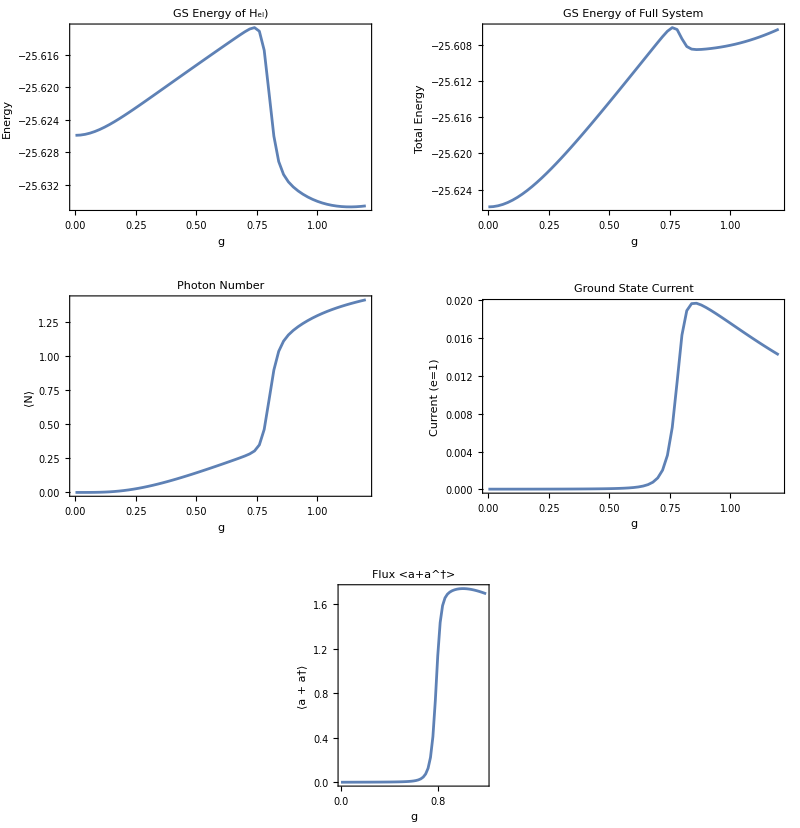

```mathematica
(*Clear previous definitions*)ClearAll["Global`*"];

(*1. Physical and Numerical Parameters*)
ED0=-0.3;                     (*Spin-up normal site energy*)
DeltaZ0=4.0;                  (*Zeeman splitting*)
t0=2.0;                       (*SC bulk hopping*)
Delta0=0.6;                   (*SC gap*)
tR0=0.5;                      (*Right hopping*)
tL0=0.5;                      (*Left hopping*)
omegaR=0.02;                   (*Cavity frequency*)

phiClassical=10^-3;      (*Classical phase*)
NumSCsites=10;                (*Number of SC sites*)
Ns=1+NumSCsites;            (*Total electronic sites (1 Normal+10 SC)*)

gmin=0.0;
gmax=1.2;
dg=0.02;                      (*g range and step*)

Nphot=200;                    (*Photon Hilbert space truncation*)
NumStepsForConvergence=20;    (*Self-consistent loop steps*)

(*2. Construct Photonic Operators in Truncated Fock Space*)
a=Table[If[j==i+1,√i//N,0],{i,1,Nphot},{j,1,Nphot}];
adag=ConjugateTranspose[a];
Nop=adag.a;                 (*Photon number operator*)
X=a+adag;                   (*Coordinate operator a+a^\dagger*)

(*3. Base Electronic Hamiltonians (excluding boundary terms)*)
hup=Table[0.0,{Ns},{Ns}];
hup[[1,1]]=ED0;
Do[hup[[j,j+1]]=-t0;hup[[j+1,j]]=-t0,{j,2,Ns-1}];
hup[[1,Ns]]=-tL0;hup[[Ns,1]]=-tL0;

hdn=Table[0.0,{Ns},{Ns}];
hdn[[1,1]]=ED0+DeltaZ0;
Do[hdn[[j,j+1]]=-t0;hdn[[j+1,j]]=-t0,{j,2,Ns-1}];
hdn[[1,Ns]]=-tL0;hdn[[Ns,1]]=-tL0;

DeltaMat=DiagonalMatrix[Join[{0.0},ConstantArray[Delta0,Ns-1]]];
TrHdn=ED0+DeltaZ0; (*Constant term from Nambu transformation*)

(*Helper function to build the BdG Hamiltonian matrix*)
GetHBdG[alpha_]:=Block[{hupM=hup,hdnM=hdn},hupM[[1,2]]=-tR0*Exp[-I*phiClassical]*Conjugate[alpha];
hupM[[2,1]]=-tR0*Exp[I*phiClassical]*alpha;
hdnM[[1,2]]=-tR0*Exp[-I*phiClassical]*Conjugate[alpha];
hdnM[[2,1]]=-tR0*Exp[I*phiClassical]*alpha;
ArrayFlatten[{{hupM,DeltaMat},{DeltaMat,-Conjugate[hdnM]}}]];

(*4. Main Self-Consistent Calculation Loop*)
alpha=1.0; (*Initialize mean-field parameter*)
glist=Range[gmin,gmax,dg];

Print["Starting self-consistent loop over g..."];

results=Table[(*Precompute displacement operators for the current g value*)Dop=MatrixExp[I*g*X];
Print["g=",g];
Dopdag=ConjugateTranspose[Dop];
Do[(*Step A:Solve Electronic System*)HBdG=GetHBdG[alpha];
{vals,vecs}=Eigensystem[HBdG];
vals=Re[vals];(*Strip machine-precision residual imaginary parts*)(*Calculate expectation values of boundary bonds*)chiUp=0.0;
chiDn=0.0;
Do[val=vals[[n]];
vec=vecs[[n]];
If[val<0.0,chiUp+=Conjugate[vec[[2]]]*vec[[1]]];
If[val>0.0,chiDn+=vec[[2+Ns]]*Conjugate[vec[[1+Ns]]]],{n,1,2*Ns}];
(*Calculate current-drive parameter eta*)eta=Exp[I*phiClassical]*tR0*(chiUp+chiDn);
(*Step B:Solve Cavity System*)Hph=omegaR*Nop-(eta*Dop+Conjugate[eta]*Dopdag);
{valsPh,vecsPh}=Eigensystem[Hph];
valsPh=Re[valsPh];
(*Find the index of the photonic ground state*)idx=Ordering[valsPh,1][[1]];
Eph=valsPh[[idx]];
psiPh=vecsPh[[idx]];
(*Step C:Update alpha using mixing to stabilize convergence*)alphaNew=Conjugate[psiPh].(Dop.psiPh);
alpha=0.5*alpha+0.5*alphaNew;,{step,NumStepsForConvergence}];
(*Step D:Post-convergence calculations*)Eel=Sum[If[v<0.0,v,0.0],{v,vals}]+TrHdn;
Etot=Eel+Eph+2.0*Re[eta*alpha];
NphotGS=Re[Conjugate[psiPh].(Nop.psiPh)];
XGS=Re[Conjugate[psiPh].(X.psiPh)];
CurrentGS=-2.0*Im[eta*alpha];
{g,Eel,Etot,NphotGS,CurrentGS,XGS},{g,glist}];

Print["Calculation complete."];

(*5. Extract and Plot Results*)
gData=results[[All,1]];
EelData=Transpose[{gData,results[[All,2]]}];
EtotData=Transpose[{gData,results[[All,3]]}];
NphotData=Transpose[{gData,results[[All,4]]}];
CurrentData=Transpose[{gData,results[[All,5]]}];
XData=Transpose[{gData,results[[All,6]]}];

(*Graphical output*)
GraphicsGrid[{{ListLinePlot[EelData,PlotLabel->"GS Energy of H_el)",Frame->True,FrameLabel->{"g","Energy"},ImageSize->300],ListLinePlot[EtotData,PlotLabel->"GS Energy of Full System",Frame->True,FrameLabel->{"g","Total Energy"},ImageSize->300]},{ListLinePlot[NphotData,PlotLabel->"Photon Number",Frame->True,FrameLabel->{"g","⟨N⟩"},ImageSize->300],ListLinePlot[CurrentData,PlotLabel->"Ground State Current",Frame->True,FrameLabel->{"g","Current (e=1)"},ImageSize->300]},{ListLinePlot[XData,PlotLabel->"Flux <a+a^†>",Frame->True,FrameLabel->{"g","⟨a + a†⟩"},ImageSize->300],SpanFromLeft}}]
```